```mathematica
r={Exp[t],Exp[t] Sin[t], Exp[t] Cos[t]};

dr=Assuming[Element[t,Reals],FullSimplify[D[r,t]]]
d2r=Assuming[Element[t,Reals],FullSimplify[D[r,{t,2}]]]
Assuming[Element[t,Reals],FullSimplify[dr.d2r]]
```

{ⅇ^t,ⅇ^t (Cos[t]+Sin[t]),ⅇ^t (Cos[t]-Sin[t])}

{ⅇ^t,2 ⅇ^t Cos[t],-2 ⅇ^t Sin[t]}

3 ⅇ^(2 t)

```mathematica
r={Cos[t],Sin[t],1-Sin[t]};
v=D[r,t]
a=D[r,{t,2}]
```

{-Sin[t],Cos[t],-Cos[t]}

{-Cos[t],-Sin[t],Sin[t]}

```mathematica
aTan=Assuming[Element[t,Reals],FullSimplify[v.a/Norm[v]]]
T=v/Norm[v];
```

-(√2 Cos[t] Sin[t])/(√(3+Cos[2 t]))

{-Sin[t]/(√(2 Abs[Cos[t]]^2+Abs[Sin[t]]^2)),Cos[t]/(√(2 Abs[Cos[t]]^2+Abs[Sin[t]]^2)),-Cos[t]/(√(2 Abs[Cos[t]]^2+Abs[Sin[t]]^2))}

```mathematica
aNorm=Assuming[Element[t,Reals],FullSimplify[Norm[Cross[v,a]]/Norm[v]]]
NN=D[T,t]/Norm[D[T,t]];
```

2/(√(3+Cos[2 t]))

-Graphics3D-

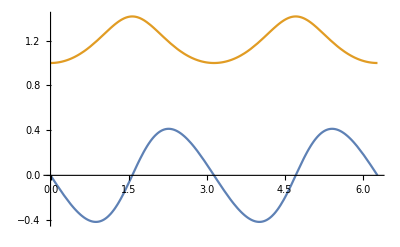

{-Cos[t],-Sin[t],Sin[t]}

True

```mathematica
ParametricPlot3D[{r,T,NN},{t,0,2Pi}]
Plot[{aTan,aNorm},{t,0,2Pi}]

Assuming[Element[t,Reals],FullSimplify[aTan T + aNorm NN]]
%==a
```